# 1st/2nd Order Ep and SEexp for FP Polaron

## Parameters and Equations

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx
μ= -2.2;
α=2;
```

## 1st Order

## Q Integral

```mathematica
Integrand[ω_, q1_,τ_] := 1/(2*Pi)^3*vq2FP[q1]*dqFP[0,τ]*g0[q1,0,τ]*Exp[(ω-μ)*τ];
```

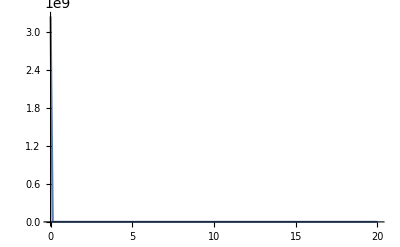

```mathematica
Plot[Integrand[-2,q1,0.5],{q1,0,20}, PlotPoints->10, MaxRecursion->4, PlotRange->Full]
```

```mathematica
seexp[ω_,τ_]:=NIntegrate[4*Pi*q1^2*Integrand[ω,q1,τ],{q1,0,qc} ];
```

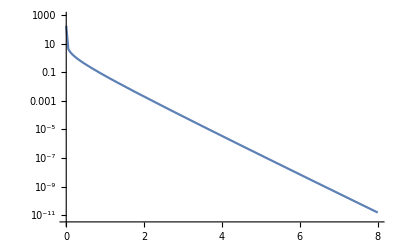

```mathematica
LogPlot[seexp[-2,τ],{τ,0,8}, PlotPoints->10, MaxRecursion->4, PlotRange->Full, PlotLegends->"SeExp"]
```

## Integrating over tau

```mathematica
Ep[ω_]:=NIntegrate[4*Pi*q1^2*Integrand[ω,q1,τ],{q1,0,qc},{τ,0,10} ];
```

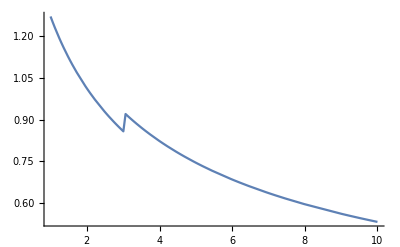

```mathematica
Plot[Ep[-w], {w,1,10},PlotPoints->10, MaxRecursion->4, PlotRange->Full]
```

## Data Output

```mathematica
omega2 = Table[{τ, seexp[-2,τ]},{τ, 0, 1.5, 0.01}];
```

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/FP"];
DumpSave["FP_1st_seexpmut.mx", {omega2}];
Export["mat_FP_1st_seexpmut_w2", omega2, "Table"];
```

## 2nd Order Rainbow

```mathematica
Integrand[ω_, q1_,q2_,τ_,τ1_,τ2_, costheta_ ] := 1/(2*Pi)^6*vq2FP[q1]*vq2FP[q2]*dqFP[0,τ]*dqFP[τ1,τ2]*g0[q1,0,τ1]*g0[q1,τ2,τ]*g0cos[q1, q2, τ1,τ2,costheta]*Exp[(ω-μ)*τ];
```

## τ Integral

```mathematica
f[ω_, q1_,q2_,τ_, costheta_ ]:= Integrate[Integrand[ω, q1,q2,τ,τ1,τ2, costheta],{τ2,0,τ},{τ1,0,τ2}];
```

## Q Integral

```mathematica
qmax=100;
seexp2nd[ω_,τ_]:=NIntegrate[4*Pi*q1^2*2*Pi*q2^2*f[ω, q1,q2,τ, costheta],{q1,0,qmax},{costheta,-1,1},{q2,0,qmax} ];
```

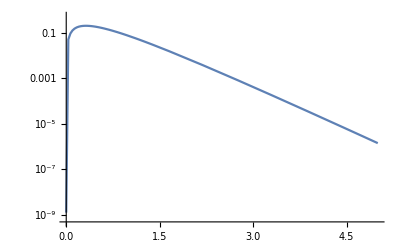

```mathematica
LogPlot[seexp2nd[-2, τ],{τ,0,5}, PlotPoints->10, MaxRecursion->4, PlotRange->Full]
```

## Data Output

```mathematica
omega22nd = Table[{τ, seexp2nd[-2,τ]},{τ, 0, 1.5, 0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/FP"];
DumpSave["FP_2nd_seexpmut.mx", {omega22nd}];
Export["mat_FP_2nd_seexpmut_w2", omega22nd, "Table"];
```

## 1st Order G

```mathematica
Integrand[τ_,τ1_,τ2_,q1_] := 1/(2*Pi)^3*vq2FP[q1]*dqFP[τ1,τ2]*g0[0,0,τ1]*g0[q1,τ1,τ2]*g0[0,τ2,τ];
f[τ_,q1_ ]:= Integrate[Integrand[τ,τ1,τ2,q1],{τ2,0,τ},{τ1,0,τ2}];
```

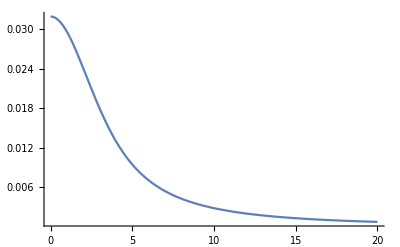

```mathematica
Plot[4*Pi*q1^2*f[0.5,q1],{q1,0,20}, PlotPoints->10, MaxRecursion->4, PlotRange->Full]
```

```mathematica
g1[τ_]:=NIntegrate[4*Pi*q1^2*f[τ,q1],{q1,0,qc} ];
```

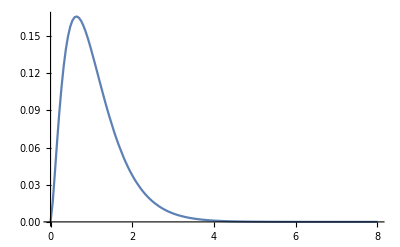

```mathematica
Plot[g1[τ],{τ,0,8}, PlotPoints->10, MaxRecursion->4, PlotRange->Full, PlotLegends->"g1"]
```

## Data Output

```mathematica
g1data= Table[{τ, g1[τ]},{τ, 0, 5, 0.1}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/FP"];
Export["mat_FP_g1", g1data, "Table"];
```